# Guard extraction: termination, soundness, completeness — Findings (v0)

## gtpyhop-diagnostics, commit caa3a1b: atoms come straight from the success analysis

type: findings
topic: diagnostics_guard_cf
date: 2026-11-17
version: v0
prior-version: round 00 (00-findings_guard_control_flow_v0), commit dc3f852
key-metric: necessary literals missed where tests are independent and no success return is inside a loop: 0 of every action body of ≤ 6 statements
decision-required: confirm

## Headline Result

metric:    bodies where the atoms are not exactly the necessary literals, tests independent, no success return inside a loop
value:     0 of 80,443  (caa3a1b)
unit:      action bodies
prior:     not established (round 00 proved soundness only)
direction: down

Round 00 proved that dc3f852 never reports an atom that a successful run can violate (soundness: no false positives). This round asks the converse, and two practical questions around it: does the analysis always finish, does it report every precondition it could (completeness: no missed true positives), and what does a reported atom guarantee to whoever acts on it. Answering the second found a gap: dc3f852 dropped requirements the analysis had proved whenever the failing side of an if was not spelled return False. caa3a1b closes it by emitting atoms straight from the analysis, and changes no atom on the bundled examples or the 436-domain corpus.

## Model

The model is round 00's, unchanged: inert statements ok (return state), bail (return False, None, bare return, raise), eff (an effect), if[id, t, A, B] and loop[id, A], over tests p, q, r. sem[P, False] is the condition under which the action succeeds. an mirrors guards._required_on_success and returns {mayOk, R}: whether the block may succeed, and the set R of (if, polarity) pairs that every successful path passes. dc3f852 reported R filtered by the old per-if reading; caa3a1b reports R itself.

Vocabulary. A literal is one if test with a direction, t or not t. A literal is necessary when every successful run satisfies it, i.e. sem ⟹ literal. Soundness: every reported literal is necessary. Completeness: every necessary literal is reported. A body that can never succeed makes every literal vacuously necessary; such atoms say nothing, and are counted apart.

## Results Tables

### R1. Termination and cost

an recurses only on strictly smaller terms: the rest of a statement list, or the branches of an if. Every recursion therefore stops, by structural induction, with no fixpoint iteration: a loop is summarised in one step by scanning its body for a success return (succIn), never iterated. Each statement outside a loop body costs one step, so the analysis is linear in the number of statements; the Python code adds one scan of the subtree under each loop, with or try, so at most statements × nesting depth.

```mathematica
{Length[progs],Max[((#1["steps"])/(#1["size"])&)/@prof],AllTrue[prof,#1["steps"]≤#1["size"]&]}
```

{94350,1,True}

Bodies checked, the largest ratio of analysis steps to statements, and whether every body stays within one step per statement.

### R2. Soundness carries over

Round 00 R2 proved, by induction on the statement list, that every literal in R is necessary and that mayOk = False only for bodies that cannot succeed. Its last row covered the filter dc3f852 applied (kept ⊆ R); caa3a1b keeps all of R, the case kept = R, so the proof applies unchanged. Exhaustive re-check: atoms reported by each reading, split into sound and informative (the body can succeed), vacuous (it cannot), and unsound.

```mathematica
tbl[{"reading","sound, informative","vacuous","unsound"},{Prepend[fmt/@tWalk,"ast.walk (0.1.1)"],Prepend[fmt/@tDc,"filtered (dc3f852)"],Prepend[fmt/@tCur,"analysis (caa3a1b)"]}]
```

reading | sound, informative | vacuous | unsound
ast.walk (0.1.1) | 17,085 | 34,173 | 13,890
filtered (dc3f852) | 13,566 | 4,116 | 0
analysis (caa3a1b) | 54,252 | 9,768 | 0

### R3. Completeness, relative to independent tests

Theorem. If no two ifs read related tests and no success return is inside a loop, then for every body: mayOk is True exactly when the body can succeed, and R is exactly the set of necessary literals.

Proof, by the same induction as round 00, with the invariant strengthened from ⊆ to =. Write Impl(f) for the literals f implies. Two lemmas carry every clause. L1: a literal follows from X or Y exactly when it follows from both, so Impl(X ∨ Y) = Impl(X) ∩ Impl(Y). L2: if t occurs nowhere in a satisfiable X, then Impl(t ∧ X) = {t} ∪ Impl(X), because any assignment satisfying X can be extended with t = True. For an if, the success condition is (t ∧ A) ∨ (¬t ∧ B): by L1 and L2 its literals are Impl(A) ∩ Impl(B) when both branches can succeed (t and ¬t cancel), {¬t} ∪ Impl(B) when only B can, and symmetrically. These are the analysis' three if rules. A loop with no success return inside has condition (c ∧ A) ∨ (¬c ∧ k) with A ⟹ k (round 00's lemma), so its if literals are Impl(k): the analysis passes the continuation through. A loop with a success return inside is where the theorem stops: the analysis returns nothing, while the loop's own guards may be necessary.

```mathematica
tbl[{"obligation","checked as","result"},{{"L1: Impl(X ∨ Y) = Impl(X) ∩ Impl(Y)","propositional tautology",mark[TautologyQ[(x||y⇒l)⧦(x⇒l)&&(y⇒l),{x,y,l}]]},{"L2: Impl(t ∧ X) = {t} ∪ Impl(X), t fresh","every satisfiable X of two variables, every literal",mark[AllTrue[Select[U,SatisfiableQ],ex[t&&#1,litsOf[{a,b,t}]]==={True,Sort[ex[#1,litsOf[{a,b}]]⟦2⟧∪{t}]}&]]},{"if rule = exact literals of (t ∧ A) ∨ (¬t ∧ B)","every pair A, B of two-variable functions (256)",mark[AllTrue[Tuples[{U,U}],ifRule[ex[#1⟦1⟧,litsOf[{a,b}]],ex[#1⟦2⟧,litsOf[{a,b}]]]===ex[(t&&#1⟦1⟧)||(!t&&#1⟦2⟧),litsOf[{a,b,t}]]&]]},{"loop rule = exact if literals of (c ∧ A) ∨ (¬c ∧ k), A ⟹ k","every such pair A, k",mark[AllTrue[Select[Tuples[{U,U}],TautologyQ[#1⟦1⟧⇒#1⟦2⟧,{a,b}]&],ex[#1⟦2⟧,litsOf[{a,b}]]===ex[(cc&&#1⟦1⟧)||(!cc&&#1⟦2⟧),litsOf[{a,b}]]&]]},{"return state, return False, effect","f = True, False, k","immediate"}}]
```

obligation | checked as | result
L1: Impl(X ∨ Y) = Impl(X) ∩ Impl(Y) | propositional tautology | proved
L2: Impl(t ∧ X) = {t} ∪ Impl(X), t fresh | every satisfiable X of two variables, every literal | proved
if rule = exact literals of (t ∧ A) ∨ (¬t ∧ B) | every pair A, B of two-variable functions (256) | proved
loop rule = exact if literals of (c ∧ A) ∨ (¬c ∧ k), A ⟹ k | every such pair A, k | proved
return state, return False, effect | f = True, False, k | immediate

L1 is proved by TautologyQ. L2 and the two rules are proved by hand above; the rows check them over a finite universe as a guard against a slip in the argument. Exhaustive check on the programs themselves, with each if's test replaced by its own fresh variable (independence), against the literals the success condition implies:

```mathematica
tbl[{"bodies","count","analysis = exact","analysis ⊆ exact"},{{"no success return inside a loop",fmt[Length[eligible]],fmt[exactCount],"—"},{"a success return inside a loop",fmt[Length[inLoopP]],fmt[Count[inLoopP,pr_/;{pr["an"]⟦1⟧,Sort[pr["an"]⟦2⟧]}===pr["exact"]]],fmt[Count[inLoopP,pr_/;SubsetQ[pr["exact"]⟦2⟧,pr["an"]⟦2⟧]]]}}]
```

bodies | count | analysis = exact | analysis ⊆ exact
no success return inside a loop | 80,443 | 80,443 | —
a success return inside a loop | 13,907 | 6,752 | 13,907

### R4. Where completeness stops, with the real tests

With the real tests p, q, r a test may repeat, which independence excludes. Every necessary literal the analysis misses, in bodies that can succeed, by cause:

```mathematica
tbl[{"cause","literals missed","smallest example","literal"},{({"a success return inside a loop, or the if inside one",fmt[Length[missLoop]],showP[#1⟦1⟧],ToString[lit@@#1,InputForm]}&)[First[SortBy[missLoop,LeafCount]]],({"a test read twice on one path",fmt[Length[missRep]],showP[#1⟦1⟧],ToString[lit@@#1,InputForm]}&)[First[SortBy[missRep,LeafCount]]],{"anything else",fmt[Length[missed]-Length[missLoop]-Length[missRep]],"—","—"}}]
```

cause | literals missed | smallest example | literal
a success return inside a loop, or the if inside one | 12,954 | {loop[{if[p, {}, {ok}]}]} |  !p
a test read twice on one path | 11,352 | {if[p, {}, {if[p, {ok}, {ok}]}]} |  !p
anything else | 0 | — | —

"Anything else" is 0, as the theorem predicts. Both causes have known remedies at a price: following loops needs dominance on a control-flow graph rather than one pass over the syntax tree, and correlated tests need a path-sensitive analysis, exponential in the worst case. In real domains a loop's guards usually read the loop variable, which no trace binds, so they could not be evaluated anyway.

The gap caa3a1b closes: literals the analysis proved but dc3f852's per-if reading dropped, all of them sound by R2.

```mathematica
tbl[{"literals gained","in bodies","smallest example","literal"},{({fmt[Length[gained]],fmt[Length[DeleteDuplicates[gained⟦All,1⟧]]],showP[#1⟦1⟧],ToString[lit@@#1,InputForm]}&)[First[SortBy[gained,LeafCount]]]}]
```

literals gained | in bodies | smallest example | literal
46,338 | 27,654 | {if[p, {}, {ok}]} |  !p

In the smallest, the if branch is empty (pass) and the action then falls off the end, returning None: success needs not p, yet no return False in the if says so.

### R5. What a reported atom guarantees

Corollary (necessity). If a reported atom is false in some state, the action fails there, and it fails in every state where that atom stays false. Any repair must make it true; repairing anything else alone cannot suffice. This is soundness read from the consumer's side.

Limit 1, one way only: fixing every reported atom does not ensure success. Here success needs p and (q or r), so R = {p}; with p true and q, r false every atom holds, yet the action fails.

```mathematica
With[{P=number[{sIf[p,{sIf[q,{ok},{}],sIf[r,{ok},{}]},{}],bail}]},{showP[P],showReq[P,cur[P]],sem[P,False]/.{p->True,q->False,r->False}}]
```

{{if[p, {if[q, {ok}, {}], if[r, {ok}, {}]}, {}], bail},p,False}

Limit 2, no list of atoms can be complete: when success needs one of two alternatives, no single literal is necessary. Here success is p or q, the only sound set of atoms is empty, and a complete explanation would have to say p ∨ q.

```mathematica
With[{P=number[{sIf[p,{ok},{}],sIf[q,{ok},{}],bail}]},{showP[P],BooleanMinimize[sem[P,False]],cur[P]}]
```

{{if[p, {ok}, {}], if[q, {ok}, {}], bail},p||q,{}}

Limit 3, outside the theorem: a missed necessary literal (R4) is as necessary as a reported one. Under the theorem's hypotheses there are none, and the split is exact: reported means necessary, unreported means some successful run does without it.

### R6. The code computes the model

As round 00 R5, for the two latest readings: scripts/cf_agree.py renders every program as a Python action, runs extract_action_guards from dc3f852 and from caa3a1b, and compares their atoms with the model's (newReq and cur respectively).

```mathematica
Module[{json=FileNameJoin[{$TemporaryDirectory,"guard_r01_programs.json"}],old=FileNameJoin[{$TemporaryDirectory,"guard_r01_old.py"}],new=FileNameJoin[{$TemporaryDirectory,"guard_r01_new.py"}],res},Export[json,(Association["prog"->toJ[#1],"old"->newReq[#1],"new"->cur[#1]]&)/@progs,"RawJSON","Compact"->True];WriteString[old,RunProcess[{"git","-C",$repo,"show","dc3f852:packages/gtpyhop-diagnostics/src/gtpyhop/diagnostics/guards.py"},"StandardOutput"]];Close[old];WriteString[new,RunProcess[{"git","-C",$repo,"show","caa3a1b:packages/gtpyhop-diagnostics/src/gtpyhop/diagnostics/guards.py"},"StandardOutput"]];Close[new];res=RunProcess[{"python3","-S",FileNameJoin[{$here,"scripts","cf_agree.py"}],old,new,json}];DeleteFile[{json,old,new}];{res["ExitCode"],StringTrim[res["StandardOutput"]]}]
```

{0,programs=94350 old_mismatches=0 new_mismatches=0}

## Observations

Signal | Baseline / Expected | Observed [source] | Interpretation
termination | always, linear | ≤ 1 step per statement on every body [R1] | structural recursion, no fixpoint
unsound atoms | 0 | 0 [R2] | soundness carries over from round 00
completeness | exact under the hypotheses | 80,443 of 80,443 exact [R3] | the theorem holds up to the bound, and by proof beyond it
misses, real tests | only loops and repeated tests | 12,954 + 11,352, other 0 [R4] | the two known costs, nothing else
per-if gap | closed | 46,338 literals gained [R4] | none occur in the bundled examples or the corpus
model vs code | 0 mismatches | 0 and 0 [R6] | the proof covers the shipped guards.py

### Scope: what this does not prove

Tests are read on the state the action was called on. A test that reads state the action has already changed is outside the model, for soundness and completeness alike.

Completeness is relative: to independent tests, to success returns outside loops, and to the literals of if tests. Round 00's splitting of each requirement into atoms is a separate step with its own precision.

The bundled and corpus counts are measurements (diagnostics_guard_nnf/scripts), listed in the commit message: no atom changes between dc3f852 and caa3a1b, recognition 330 of 335 and 5,807 of 5,885.

## Charts & Visualizations

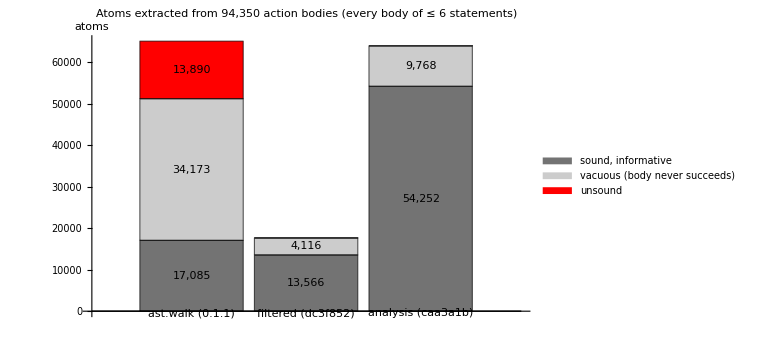

```mathematica
BarChart[{tWalk,tDc,tCur},ChartLayout->"Stacked",ChartLabels->{{"ast.walk (0.1.1)","filtered (dc3f852)","analysis (caa3a1b)"},None},ChartLegends->Placed[{"sound, informative","vacuous (body never succeeds)","unsound"},Below],ChartStyle->{GrayLevel[0.45],GrayLevel[0.8],Red},AxesLabel->{None,"atoms"},LabelingFunction->(If[#1>2000,Placed[Style[fmt[#1],Black,11],Center],None]&),PlotLabel->"Atoms extracted from "<>fmt[Length[progs]]<>" action bodies (every body of ≤ "<>ToString[$maxSize]<>" statements)",ImageSize->560]
```

Caption: dc3f852 removes every unsound atom (red) and most vacuous ones (light grey), and loses informative atoms (dark grey, 17,085 to 13,566) in loops and repeated tests. caa3a1b stays sound and reports 54,252 informative atoms: most enumerated bodies fail by falling through, which the per-if reading of both earlier versions could not see (R4). Real domains spell their failures as return False, so there dc3f852 and caa3a1b give the same atoms.

## Contradictions & Surprises

Round 00 attributed every precision loss to loops and repeated tests. That was true of the atoms dc3f852 dropped relative to 0.1.1, but both versions shared a third, larger miss: the per-if reading never produced an atom for an if whose failing side falls through. It shows up only when completeness is measured against the success condition rather than against the previous version.

Closing it changed nothing measurable in practice: every bundled and corpus action already spells its failing side as a return.

## Steering Questions

[now] Keep caa3a1b in the same PR as dc3f852? It turns the proof from sound into sound and relatively complete, and removes the per-if classifier.

[next run] Make the consumer contract explicit to whoever reads explain_dead_end (an agent, a person): a false atom is necessary, the list is not sufficient, and alternatives are never atoms. A separate change.

[next run] A test that reads state the action has already written. Measure how often it occurs before deciding whether to model writes.

## References

G. A. Kildall, A unified approach to global program optimization, POPL 1973. The dataflow framework: the analysis is a backward must-analysis, meet = intersection.

T. Lengauer, R. E. Tarjan, A fast algorithm for finding dominators in a flowgraph, ACM TOPLAS 1(1), 1979. R is the set of branch edges that dominate every success return.

K. D. Cooper, T. J. Harvey, K. Kennedy, A simple, fast dominance algorithm, Software: Practice and Experience, 2001. The iterative form, which a control-flow-graph version would use to recover R4's loop literals.

P. Cousot, R. Cousot, M. Fähndrich, F. Logozzo, Automatic inference of necessary preconditions, VMCAI 2013, LNCS 7737. The same goal: conditions whose violation guarantees failure.

M. Das, S. Lerner, M. Seigle, ESP: path-sensitive program verification in polynomial time, PLDI 2002. A route to R4's repeated-test literals.

## Pointers

Commits dc3f852 (sound), caa3a1b (complete), on top of round 00 of diagnostics_guard_nnf

tools/diagnostics_guard_check.py: 16 cases, including the executed soundness and completeness property cases

Round 00 of this topic: 00-findings_guard_control_flow_v0, whose build pins dc3f852

## Appendix: definitions (initialization cells)

Round 00's model (sem, an, oldReq, newReq, the enumeration), with an counting its steps in $steps. cur is the caa3a1b reading, fresh gives every if its own test, exact the literals the success condition then implies, profile one truth table per program. U, ex and ifRule are the finite universe of R3.

```mathematica
tests={p,q,r}
```

```mathematica
sem[{},k_]:=k
```

```mathematica
sem[{ok,___},k_]:=True
```

```mathematica
sem[{bail,___},k_]:=False
```

```mathematica
sem[{eff,rest___},k_]:=sem[{rest},k]
```

```mathematica
sem[{if[i_,t_,A_,B_],rest___},k_]:=With[{kk=sem[{rest},k]},(t&&sem[A,kk])||(!t&&sem[B,kk])]
```

```mathematica
sem[{loop[i_,A_],rest___},k_]:=With[{kk=sem[{rest},k]},(c[i]&&sem[A,kk])||(!c[i]&&kk)]
```

```mathematica
succIn[A_]:=!FreeQ[A,ok]
```

```mathematica
an[{},st_]:=st
```

```mathematica
an[{s_,rest___},st_]:=(++$steps;step[s,an[{rest},st]])
```

```mathematica
step[ok,_]:={True,{}}
```

```mathematica
step[bail,_]:={False,{}}
```

```mathematica
step[eff,st_]:=st
```

```mathematica
step[if[i_,t_,A_,B_],st_]:=Module[{a=an[A,st],b=an[B,st]},Which[!a⟦1⟧&&!b⟦1⟧,{False,{}},!a⟦1⟧,{True,b⟦2⟧∪{{i,True}}},!b⟦1⟧,{True,a⟦2⟧∪{{i,False}}},True,{True,a⟦2⟧∩b⟦2⟧}]]
```

```mathematica
step[loop[i_,A_],st_]:=If[succIn[A],{True,{}},st]
```

```mathematica
topBail[A_]:=MemberQ[A,bail]
```

```mathematica
oldPol[if[i_,t_,A_,B_]]:=Which[topBail[A],True,succIn[A],False,B=!={}&&topBail[B],False,True,None]
```

```mathematica
ifs[P_]:=Cases[P,_if,∞]
```

```mathematica
testOf[P_,i_]:=FirstCase[P,if[i,t_,__]:>t,Missing[],∞]
```

```mathematica
oldReq[P_]:=DeleteCases[({#1⟦1⟧,oldPol[#1]}&)/@ifs[P],{_,None}]
```

```mathematica
newReq[P_]:=oldReq[P]∩an[P,{False,{}}]⟦2⟧
```

```mathematica
lit[P_,{i_,neg_}]:=If[neg,!testOf[P,i],testOf[P,i]]
```

```mathematica
vars[P_]:=Join[tests,Cases[P,loop[i_,_]:>c[i],∞]]
```

```mathematica
stmts[1]={ok,bail,eff}
```

```mathematica
stmts[n_/;n≥2]:=stmts[n]=Join[Flatten[Table[Outer[sIf,tests,blocks[m],blocks[n-1-m],1],{m,0,n-2}],3],sLoop/@blocks[n-1]]
```

```mathematica
blocks[0]={{}}
```

```mathematica
blocks[n_/;n≥1]:=blocks[n]=Select[Flatten[Table[Outer[Prepend[#2,#1]&,stmts[m],blocks[n-m],1],{m,1,n}],2],FreeQ[Most[#1],ok|bail]&]
```

```mathematica
nb[l_List]:=nb/@l
```

```mathematica
nb[sIf[t_,A_,B_]]:=With[{i=++$id},if[i,t,nb[A],nb[B]]]
```

```mathematica
nb[sLoop[A_]]:=With[{i=++$id},loop[i,nb[A]]]
```

```mathematica
nb[s_]:=s
```

```mathematica
number[P_]:=Block[{$id=0},nb[P]]
```

```mathematica
tt[f_,v_]:=Boole[BooleanTable[f,v]]
```

```mathematica
necessary[P_,req_]:=With[{v=vars[P]},With[{S=tt[sem[P,False],v]},Select[req,Min[1-S+tt[lit[P,#1],v]]==1&]]]
```

```mathematica
checkProg[P_]:=checkProg[P]=Module[{st=an[P,{False,{}}],o=oldReq[P],n=newReq[P]},{1,Length[o],Length[o]-Length[necessary[P,o]],Length[n],Length[n]-Length[necessary[P,n]],Length[st⟦2⟧]-Length[necessary[P,st⟦2⟧]],Boole[!st⟦1⟧&&Max[tt[sem[P,False],vars[P]]]==1],Boole[!SubsetQ[o,n]]}]
```

```mathematica
satisfiable[P_]:=Max[tt[sem[P,False],vars[P]]]==1
```

```mathematica
inLoop[P_,i_]:=!FreeQ[Cases[P,loop[_,A_]:>A,∞],if[i,___]]
```

```mathematica
repeats[P_]:=!DuplicateFreeQ[Cases[P,if[_,t_,__]:>t,∞]]
```

```mathematica
T[f_,v_]:=TautologyQ[f,v]
```

```mathematica
inv[f_,okq_,R_]:=(f⇒And@@R)&&(!okq⇒!f)
```

```mathematica
showP[P_]:=ToString[Replace[P,{if[i_,t_,A_,B_]:>if[t,A,B],loop[i_,A_]:>loop[A]},All],InputForm]
```

```mathematica
showReq[P_,req_]:=Row[Riffle[(ToString[lit[P,#1],InputForm]&)/@req,",  "]]
```

```mathematica
colour[P_,req_]:=Row[Riffle[(With[{s=ToString[lit[P,#1],InputForm]},If[necessary[P,{#1}]==={#1},s,Style[s,Red]]]&)/@req,",  "]]
```

```mathematica
tbl[headers_,rows_]:=Grid[Prepend[rows,(#1&)/@headers],Frame->All,Alignment->Left,Background->{None,{GrayLevel[0.9]}},Spacings->{1.2,0.6}]
```

```mathematica
mark[b_]:=If[TrueQ[b],Style["proved",Darker[Green]],Style["fails",Red]]
```

```mathematica
toJ[ok]="ok"
```

```mathematica
toJ[bail]="bail"
```

```mathematica
toJ[eff]="eff"
```

```mathematica
toJ[l_List]:=toJ/@l
```

```mathematica
toJ[if[i_,t_,A_,B_]]:={"if",i,ToString[t],toJ[A],toJ[B]}
```

```mathematica
toJ[loop[i_,A_]]:={"loop",i,toJ[A]}
```

```mathematica
cur[P_]:=an[P,{False,{}}]⟦2⟧
```

```mathematica
ifLits[P_]:=Flatten[({{#1,True},{#1,False}}&)/@Cases[P,if[i_,___]:>i,∞],1]
```

```mathematica
succInLoop[P_]:=!FreeQ[Cases[P,loop[_,A_]:>A,∞],ok]
```

```mathematica
size[P_]:=Count[P,ok|bail|eff|_if|_loop,{1,∞}]
```

```mathematica
steps[P_]:=Block[{$steps=0},an[P,{False,{}}];$steps]
```

```mathematica
fresh[P_]:=Replace[P,if[i_,_,A_,B_]:>if[i,f[i],A,B],All]
```

```mathematica
exact[P_]:=With[{Q=fresh[P]},With[{v=Join[Cases[Q,if[i_,___]:>f[i],∞],Cases[Q,loop[i_,_]:>c[i],∞]]},With[{S=tt[sem[Q,False],v]},If[Max[S]==0,{False,{}},{True,Sort[Select[ifLits[Q],Min[1-S+tt[If[#1⟦2⟧,!f[#1⟦1⟧],f[#1⟦1⟧]],v]]==1&]]}]]]]
```

```mathematica
profile[P_]:=profile[P]=Module[{v=vars[P],S,ok},S=tt[sem[P,False],v];ok=Max[S]==1;Association["ok"->ok,"loop"->succInLoop[P],"steps"->steps[P],"size"->size[P],"nec"->If[ok,Select[ifLits[P],Min[1-S+tt[lit[P,#1],v]]==1&],{}],"walk"->oldReq[P],"dc"->newReq[P],"cur"->cur[P],"an"->an[P,{False,{}}],"exact"->exact[P]]]
```

```mathematica
split[pr_,key_]:=With[{atoms=pr[key]},If[pr["ok"],{Length[atoms∩pr["nec"]],0,Length[Complement[atoms,pr["nec"]]]},{0,Length[atoms],0}]]
```

```mathematica
U=Table[BooleanFunction[k,{a,b}],{k,0,15}]
```

```mathematica
litsOf[vs_]:=Join[vs,Not/@vs]
```

```mathematica
ex[g_,ls_]:=If[SatisfiableQ[g],{True,Sort[Select[ls,TautologyQ[g⇒#1,{a,b,t,cc}]&]]},{False,{}}]
```

```mathematica
ifRule[{oa_,ra_},{ob_,rb_}]:=Which[!oa&&!ob,{False,{}},!oa,{True,Sort[rb∪{!t}]},!ob,{True,Sort[ra∪{t}]},True,{True,Sort[ra∩rb]}]
```